```mathematica
SetDirectory["C:\\Python32\\HeatBumpGUI\\mathematica_output"];
```

```mathematica
absorbed={#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧)/(1*^9)}&/@Import["absorbed_power_density.dat"];
transmitted={#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧)/(1*^9)}&/@Import["transmitted_power_density.dat"];
filter={#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧)/(1*^9)}&/@Import["filter_power_density.dat"];
source={#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧)/(1*^9)}&/@Import["source_power_density.dat"];
```

```mathematica
f5[data_,lim_,title_]:=GraphicsGrid[{{ListPlot3D[data,PlotRange->{{0,17},{0,4},{0,lim}}, Axes->True, AxesLabel->{"length mm", "width mm", "power density"}],ListContourPlot[data,PlotRange->{{0,16.5},{0,4},{0,lim}},Contours->10,Axes->True, AxesLabel->{"length mm", "width mm"},(*ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),*)ContourStyle->Black]
}},PlotLabel->title<>" Power Density W/mm^3"]
```

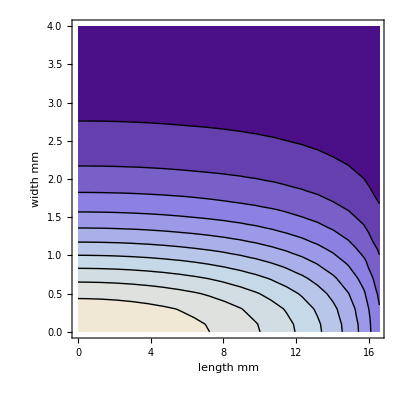

```mathematica
f5[source,21,"Source"]
```

```mathematica
Export["source.png",Rasterize[-Graphics-]]
```

source.png

```mathematica
Export["source.png",Rasterize@f5[source,21,"Source"]]
Export["filtered.png",Rasterize@f5[filter,21,"Filtered"]]
Export["absorbed.png",Rasterize@f5[absorbed,21,"Object Absorbed"]]
Export["transmitted.png",Rasterize@f5[transmitted,2,"Transmitted"]]
```

source.png

filtered.png

absorbed.png

transmitted.png

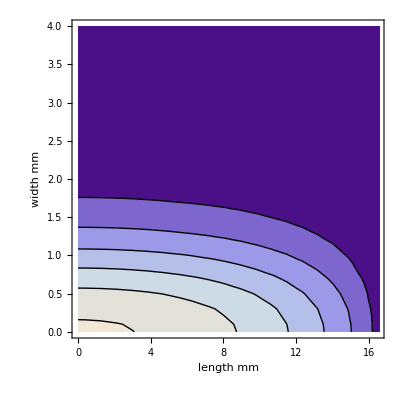
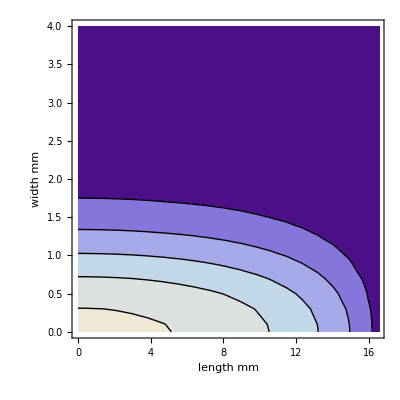
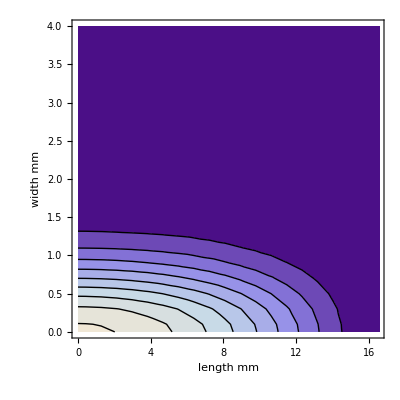
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{f5[source,21,"Source"],f5[filter,21,"Filtered"],f5[absorbed,21,"Object Absorbed"],f5[transmitted,2,"Transmitted"]}
```

```mathematica
be=Import["be.dat"];
si=Import["si.dat"];
pb=Import["pb.dat"];
cu=Import["cu.dat"];
```

```mathematica
Export["si_kedge.png",Rasterize@Show[ListPlot[si,PlotRange->{{0,20000},{0,8000}}],Graphics[{PointSize[Large],Red, Point[{ 1773.8499919704,2973.4064839298167}]}]]]
```

si_kedge.png

```mathematica
<<Units`
<<PhysicalConstants`
```

```mathematica
ws=Import["ws.dat"];
```

```mathematica
us=Delete[{#[[1]]*1000,#[[2]]}&/@Import["us.dat"],-1];
```

```mathematica
Export["wsflux.jpg",Rasterize@ListPlot[ws,Joined->True]]
```

wsflux.jpg

```mathematica
Export["usflux.jpg",Rasterize@ListPlot[us,Joined->True]]
```

usflux.jpg

```mathematica
ListPlot[ws,Joined->True]
ListPlot[us,Joined->True]
```

-Graphics-

-Graphics-

```mathematica
ea=#[[1]]&/@ws;
```

```mathematica
p[a_,n_]:=#[[n]]&/@a
```

```mathematica
flt=1
obj=10
ea=#[[1]]&/@ws;
p[a_,n_]:=#[[n]]&/@a;
```

1

10

```mathematica
wsflte=p[ws,2]*E^(-p[be,2]*flt);
wsabse=wsflte*(1-E^(-p[si,2]*obj));
wstranse=wsflte*E^(-p[si,2]*obj);
wsflt=Transpose[{ea,wsflte}];
wsabs=Transpose[{ea,wsabse}];
wstrans=Transpose[{ea,wstranse}];
```

```mathematica
usflte=p[us,2]*E^(-p[be,2]*flt);
usabse=usflte(1-E^(-p[si,2]*obj));
ustranse=usabse(E^(-p[si,2]*obj));
usflt=Transpose[{ea,usflte}];
usabs=Transpose[{ea,usabse}];
ustrans=Transpose[{ea,ustranse}];
```

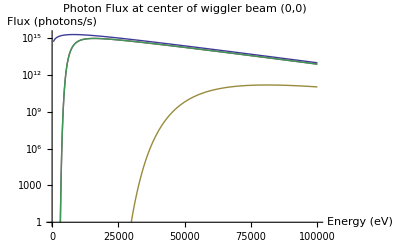

```mathematica
wig=Show[ListLogPlot[{ws,wsflt,wstrans,wsabs},PlotLabel->"Photon Flux at center of wiggler beam (0,0)",AxesLabel->{"Energy (eV)","Flux (photons/s)"},Joined->True,PlotStyle->Thick]]
```

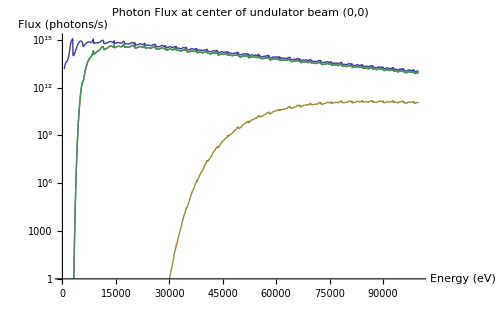

```mathematica
und=Show[ListLogPlot[{us,usflt,ustrans,usabs},PlotLabel->"Photon Flux at center of undulator beam (0,0)",AxesLabel->{"Energy (eV)","Flux (photons/s)"},Joined->True,PlotStyle->Thick]]
```

```mathematica
Export["undflux.png",Rasterize@und]
```

undflux.png

```mathematica
Export["wigflux.png",Rasterize@wig]
```

wigflux.png